All

Section

Subsection

Subsubsection

Heading

Text

TextContinued

Example

ExampleText

Equation

ExampleEquation

EquationNumber

EquationNumbered

ExampleEquationNumbered

SectionText

Homework

HomeworkText

HomeworkTextNumbered

Theorem

TheoremNumbered

TheoremContinued

TheoremNumber

ProofText

ProofContinued

Remark

Reference

Note

ItemNumbered

Lookup

InlineCell

InlineCellEditing

FigureNumbered

TableNumbered

### Editing styles

Notes (hidden cell beneath this)

Notes

Notes

Code Notes (hidden cell beneath this)

CodeNotes

CodeNotes

### Colors

### Toolbar & Course Information

```mathematica
course`number="Mathematics 212";
course`title="Differential Equations";
course`term="Fall 2019";
course`instructor="Michael Rogers";
course`dockedBG=RGBColor[0.299809,0.409247,0.780545];
course`dockedFont=RGBColor[0.972671,0.888975,0.667765];
course`dockedFrame=RGBColor[0.8050659952697032,0.1087357900358587,0.11052109559777218];
exampleBG=Graphics[{
Polygon[{{0, 0},{1,0}, {1,1}, {0, 1}}, 
VertexColors -> {White, White, Lighter@RGBColor[0.299809, 0.409247, 0.780545], Lighter@ RGBColor[0.299809, 0.409247, 0.780545]}]},
PlotRangePadding -> 0, ImagePadding->0,ImageSize -> Full,AspectRatio ->1/100];
```

```mathematica
(* Homework, index buttons *)
CellPrint[Cell[StyleData[All,"Working"],
MenuCommandKey->"D",
DockedCells->{Cell[TextData[Cell[BoxData[FormBox[
GridBox[{{
RowBox[{course`number," — ", course`term}],
course`title,
TemplateBox[{ButtonBox["\"Index\"",Appearance->"Palette",Background->RGBColor[0.972671,0.888975,0.667765],BaseStyle->{(*FontFamily->"Arial",FontSize->12,FontWeight->"Plain",*)FontColor->RGBColor[0.299809,0.409247,0.780545]},ButtonFunction:>With[{$CellContext`nb=EvaluationNotebook[]},CreatePalette[Column[Map[Button[#,NotebookLocate[{ReplaceAll["FileName",NotebookInformation[$CellContext`nb]],#}],Appearance->"Palette"]&,Union[DeleteCases[Flatten[CurrentValue[Cells[$CellContext`nb],CellTags]],Condition[Pattern[$CellContext`s,Blank[]],StringMatchQ[$CellContext`s,StringExpression["ref:",BlankSequence[]]]]]]]],WindowTitle->"Definitions",WindowElements->{"VerticalScrollBar"}]],Evaluator->Automatic,ImageSize->Automatic,Method->"Preemptive"],ButtonBox["\"Get homework\"",Appearance->"Palette",Background->RGBColor[0.972671,0.888975,0.667765],BaseStyle->{(*FontFamily->"Arial",FontSize->12,FontWeight->"Plain",*)FontColor->RGBColor[0.299809,0.409247,0.780545]},ButtonFunction:>Module[{$CellContext`n=0,$CellContext`answers},NotebookPut[Notebook[{CellGroupData[Join[{Cell[TextData[StringJoin[ReplaceAll["WindowTitle",NotebookInformation[EvaluationNotebook[]]]," — Exercises"]],"Section"]},NotebookRead[Cells[EvaluationNotebook[],CellStyle->{"Homework","HomeworkTextNumbered","HomeworkText"}]],$CellContext`answers=ReplaceAll[Map[{PreIncrement[$CellContext`n],ReplaceAll["answer",CurrentValue[#,TaggingRules]]}&,Cells[EvaluationNotebook[],CellStyle->{"HomeworkTextNumbered"}]],{Blank[],"answer"}->Sequence[]];If[Length[$CellContext`answers]>0,{CellGroupData[Join[{Cell[TextData["Answers"],"Subsection"]},ReplaceAll[$CellContext`answers,{Pattern[$CellContext`i,Blank[]],Cell[TextData[Pattern[$CellContext`data,Blank[]]],Pattern[$CellContext`opts,BlankNullSequence[]]]}:>Cell[TextData[Flatten[{StringJoin[ToString[$CellContext`i],". "],$CellContext`data}]],$CellContext`opts]]],1]},Unevaluated[Sequence[]]]]]},CellGrouping->Manual,StyleDefinitions->FrontEnd`FileName[{"diffEqClass"},"Diff Eq Style.nb"]]]],Evaluator->Automatic,ImageSize->Automatic,Method->"Preemptive"]},"RowDefault"]}},
GridBoxAlignment->{"Columns"->{Left,Center,{Right}},"ColumnsIndexed"->{},"Rows"->{{Baseline}},"RowsIndexed"->{}},GridBoxItemSize->{"Columns"->{{Scaled[0.33]}},"ColumnsIndexed"->{},"Rows"->{{1.}},"RowsIndexed"->{}}],TraditionalForm]],CellFrame->False]],
"DockedCell",
CellFrame->{{0,0},{2,0}},CellMargins->{{0,0},{4,0}},
CellBracketOptions->{"Margins"->{0,0},"Widths"->{0,0}},
CellElementSpacings->{"ClosedCellHeight"->19},
CellFrameMargins->{{10,10},{2,5}},
System`CellFrameStyle->course`dockedFrame,(*CellChangeTimes->{},*)
FontFamily->"Arial",
FontSize->12,
FontWeight->"Plain",
FontColor->course`dockedFont,
Background->course`dockedBG]},
GeneratedCell->False,
CellAutoOverwrite->False,
(*ScriptSizeMultipliers->{1.0,0.8,1.0},*)
TaggingRules->{
"CourseNumber"->course`number,
"CourseTitle"->course`title,
"CourseTerm"->course`term,
"CourseInstructor"->course`instructor,
"ExampleBackground"->exampleBG}
]]
```

All

#### TaggingRules - scratch

```mathematica
CurrentValue[EvaluationNotebook[],{TaggingRules,"ExampleBackground"}]
```

Inherited

```mathematica
TextCell[Dynamic@CurrentValue[EvaluationNotebook[],{TaggingRules,"CourseTitle"}],ShowStringCharacters->False]
```

### Dividers

```mathematica
Graphics[{Polygon[{{0,0},{1,0},{1,1},{0,1}},VertexColors->{White,White,RGBColor[0.299809,0.409247,0.780545],RGBColor[0.299809,0.409247,0.780545]}]},PlotRangePadding->0,ImageSize->Full,AspectRatio->1/50]//Deploy
```

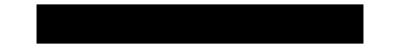

### Presentation

Subsection

Subsubsection

Heading

### Interactive Example Styles

All

Heading

Text

Input

Output

### StyleKeyMapping

```mathematica
CurrentValue[{StyleDefinitions,"Subsection",StyleKeyMapping}]
```

{Tab→Subsubsection,Backspace→Section,KeyEvent[Tab,Modifiers→{Shift}]→Section}

## Technical stuff

### File management

### Loading math212 package — obsolete

```mathematica
If[!MemberQ[$Path,NotebookDirectory[]],AppendTo[$Path, NotebookDirectory[]],$Path];
Needs["math212`"]
```

### Make index of tags

### Collect homework assignments

### Both (index/homework) together

### Lookup button (CellEventActions)

### Aligned equation grid

df | = | (cos α cos θ+sin α sin θ)√((∂f/∂x)^2+(∂f/∂y)^2)
  | = | cos(α - θ)√((∂f/∂x)^2+(∂f/∂y)^2).

### GroupOpener hint

## Click triangle to open/close

### Popup demos

### DropBox File hyperlink